# Thesis: Testing rapid helical cross-sections

Plotting the helicoid screen as a parameterized surface, intersecting it with a flat plane (caluclated from 3 coplanar points), and projecting that curve onto the xy plane.

```mathematica
c= 1;
```

```mathematica
R = 5;
```

```mathematica
x[r_,t_]:=r*Cos[t]
```

```mathematica
y[r_,t_]:=r*Sin[t]
```

```mathematica
z[t_]:=c*t
```

```mathematica
helicoid = ParametricPlot3D[{x[r,t], y[r,t], z[t]}, {t,-Pi, Pi}, {r,0,R}]
```

-Graphics3D-

```mathematica
p1 = {0,0,1};
```

```mathematica
p2 = {1,0,0};
```

```mathematica
p3 = {0,1,0};
```

```mathematica
ab = p2 - p1;
```

```mathematica
ac = p3 - p1;
```

```mathematica
normal = Cross[ab,ac]
```

{1,1,1}

```mathematica
n1 = normal[[1]]; n2 = normal[[2]]; n3 = normal[[3]];
```

```mathematica
(normal*{xx,yy,zz} - p1).{1,1,1}
```

xx+yy+zz-1

```mathematica
Simplify[(n1*xx - p1[[1]])+(n2*yy - p1[[2]])+(n3*zz - p1[[3]])]
```

xx+yy+zz-1

```mathematica
plane = ContourPlot3D[normal.{x,y,z}-p1.{1,1,1}==0,{x,-5,5},{y,-5,5},{z,-2,2},ContourStyle->Opacity[0.5],Mesh->False];
```

```mathematica
plane2= ParametricPlot3D[{x[r,t], y[r,t], z[t]}, {t,-Pi, Pi}, {r,0,R}]
```

```mathematica
points = ListPlot3D[{p1,p2,p3}, Mesh-> All];
```

```mathematica
Show[plane,points]
```

-Graphics3D-

```mathematica
Show[helicoid,plane, points]
```

-Graphics3D-

```mathematica
w[r_,t_]:=normal.{x[r,t],y[r,t],z[t]}-p1.{1,1,1}
```

```mathematica
Simplify[w[r,t]]
```

r sin(t)+r cos(t)+t-1

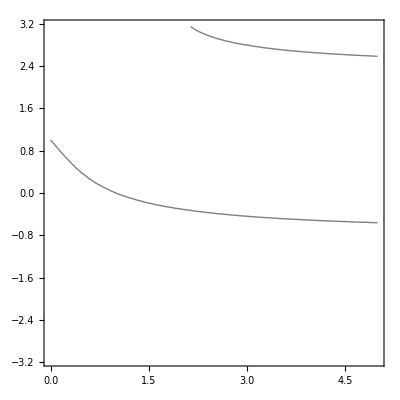

```mathematica
intersect = ContourPlot[w[r,t]==0,{r,0,5},{t,-Pi,Pi},ContourStyle->{Opacity[0.5],Thick},Mesh->False]
```

```mathematica
Show[plane,intersect]
```